```mathematica
plotLyrics[lyrics_]:=Module[{wordList,usedWords},
usedWords = {};
wordList = StringSplit[StringDelete[lyrics,","]];
MatrixPlot[Table[
If[Position[usedWords,wordList[[i]]]==={},usedWords=Append[usedWords,wordList[[i]]]];
mag = Position[usedWords,wordList[[i]]][[1,1]];
If[wordList[[i]]==wordList[[j]],mag,0],{i,Length[wordList]},{j,Length[wordList]}] 1/Length[usedWords]-.5,Frame-> None,ColorFunction->Function[{z},Hue[z,If[z==0,0,1],If[z==0,1,.75]]]]]
```

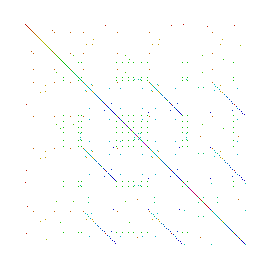

```mathematica
Lyrics="The first one I remember 
Was about three times my size
We all stood there watchin'
As Dad brought it inside
It took almost an hour
To stand it up just right
When he was done he held my Mama tight

We made cookies and hot chocolate
Sewed popcorn on a string
Cranked up the record player
So Mom could sing along with Bing
We hung candy canes and ornaments
And tinsel liberally
Turned off the light, plugged in the Chrismas tree

We can't start until it gets here
And we won't stop until it goes
It arrives on top of Dad's old Ford
But only stays a week or so
It's the one family tradition
On which we all agree
It's just not Christmas 'til we've got the tree

We wrote down what we wanted
All the bikes and guns and games
Mom set the list on fire
Sent 'em up the chimney in flames
Tucked us all in tight
Said in the morning we will see
What Santa leaves under the Christmas tree


We can't start until it gets here
And we won't stop until it goes
It arrives on top of Dad's old Ford
But only stays a week or so
It's the one family tradition
On which we all agree
It's just not Christmas 'til we've got the tree

The tree looked different in the morning
All its promise was fulfilled
Surrounded by our presents
From floor to window sill
And after all the noise and Polaroids
And shouts of joyful glee
I fell asleep under the Christmas tree


We can't start until it gets here
And we won't stop until it goes
It arrives on top of Dad's old Ford
But only stays a week or so
It's the one family tradition
On which we all agree
It's just not Christmas 'til we've got the tree";


Lyrics = StringReplace[Lyrics,"-"-> " "];
Lyrics = StringReplace[Lyrics,","-> " "];
Lyrics = StringReplace[Lyrics,"."-> " "];
Lyrics = StringReplace[Lyrics,"?"-> " "];
Lyrics = StringReplace[Lyrics,";"-> " "];
(*
Lyrics = StringReplace[Lyrics,"of"-> ""];
Lyrics = StringReplace[Lyrics,"the"-> ""];
Lyrics = StringReplace[Lyrics,"a"-> ""];
Lyrics = StringReplace[Lyrics,"are"-> ""];
Lyrics = StringReplace[Lyrics,"is"-> ""];
Lyrics = StringReplace[Lyrics,"to"-> ""];
Lyrics = StringReplace[Lyrics,"so"-> ""];
Lyrics = StringReplace[Lyrics,"no"-> ""];
Lyrics = StringReplace[Lyrics,"this"-> ""];
Lyrics = StringReplace[Lyrics,"cary"-> ""];*)
plotLyrics[Lyrics]
```

```mathematica
Despacito = Quiet[Import[NotebookDirectory[]<>"/UncleJohnsBand.mid","SoundNotes"]];
```

```mathematica
plotSong[midiData_]:=Module[{track,Instrument,NoteList,numTracks},
numTracks = Length[midiData];
Table[

track  =midiData[[α]][[335;;400]];
Instrument = track[[1,3]];
NoteList =track[[All,1]];
(*NoteList =StringDrop[track[[All,1]],-1];*)
{Instrument,ArrayPlot[Table[If[NoteList[[i]]==NoteList[[j]],1,0],{i,Length[NoteList]},{j,Length[NoteList]}],Frame-> None]},{α,2,numTracks}]]
```

```mathematica
DespacitoData = plotSong[Despacito];
Grid [Transpose[DespacitoData[[1;;-3]]]]
```

Part::take: Cannot take positions 335 through 400 in {}.

Part::partw: Part 3 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

Part::take: Cannot take positions 335 through 400 in {}.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Guitar | Bass | SteelGuitar
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Experimental code that plots based on note length*)
PlotSongWithTiming[midiData_,trackIndex_, noteIndexMin_,noteIndexMax_]:=Module[{Notes,notesUsed,xmin,xmax,ymin,ymax},
Notes  =midiData[[trackIndex]][[noteIndexMin;;noteIndexMax]];
notesUsed= {};
Do[notesUsed = Append[notesUsed,note],{note,Notes}];
{Show[
Table[
If[note1[[1]]==note2[[1]] && NumericQ[note1[[2]][[1]]+note1[[2]][[2]]+note2[[2]][[1]]+note2[[2]][[2]]],
xmin = note1[[2]][[1]];
xmax = note1[[2]][[2]];
ymin = note2[[2]][[1]];
ymax = note2[[2]][[2]];
If[True,

Graphics[{Hue[Position[notesUsed,note1[[1]]][[1,1]]/Length[notesUsed],.8,.8],Opacity[.9],Rectangle[{xmin,ymin},{xmax,ymax}]}],Nothing],Nothing]
,{note1,Notes}
,{note2,Notes}]],Sound[notesUsed]}
]
```

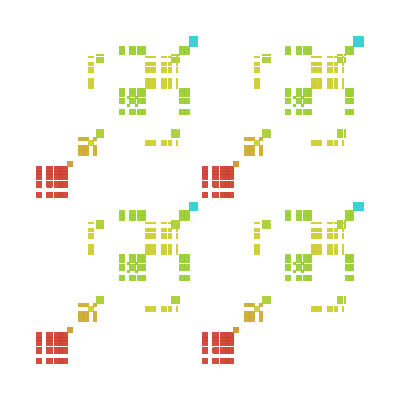
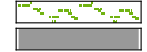

```mathematica
PlotSongWithTiming[Despacito,4,345,398]
```

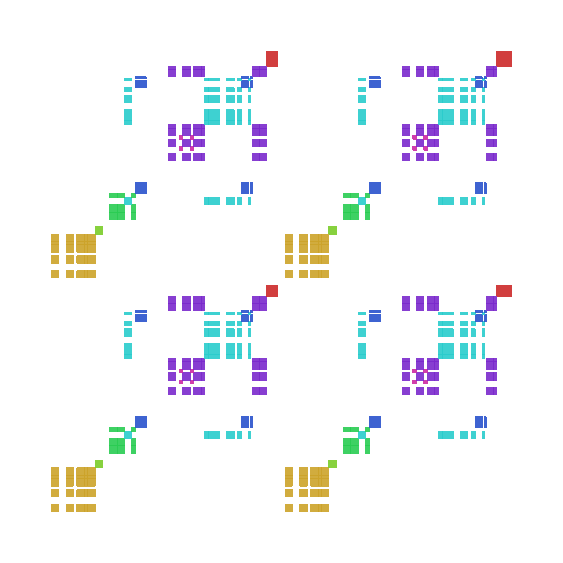

```mathematica
Show[Table[

Notes = Despacito[[trackIndex]][[345;;398]];
usedNotes = {};
Do[
If[Position[usedNotes,note1[[1]]]==={},
usedNotes = Append[usedNotes,note1[[1]]];];
,{note1,Notes}];

noteOutput = {};

instrument1 = Show[Table[noteOutput = Append[noteOutput,note2];Table[
If[note1[[1]]==note2[[1]] && NumericQ[note1[[2]][[1]]+note1[[2]][[2]]+note2[[2]][[1]]+note2[[2]][[2]]],
xmin = note1[[2]][[1]];
xmax = note1[[2]][[2]];
ymin = note2[[2]][[1]];
ymax = note2[[2]][[2]];
If[True,

Graphics[{Hue[Position[usedNotes,note1[[1]]][[1,1]]/Length[usedNotes],.8,.8],Opacity[.9],Rectangle[{xmin,ymin},{xmax,ymax}]}],Nothing],Nothing]
,{note1,Notes}]
,{note2,Notes}]]
,{trackIndex,4,4}]]
```

```mathematica
Notes = Despacito[[2]][[;;]];
usedNotes = {}
Do[
If[Position[usedNotes,note1[[1]]]==={},
usedNotes = Append[usedNotes,note1[[1]]];];
,{note1,Notes}];



instrument1 = Show[Table[
If[note1[[1]]==note2[[1]] && NumericQ[note1[[2]][[1]]+note1[[2]][[2]]+note2[[2]][[1]]+note2[[2]][[2]]],
xmin = note1[[2]][[1]];
xmax = note1[[2]][[2]];
ymin = note2[[2]][[1]];
ymax = note2[[2]][[2]];
If[Not[xmax-xmin>10 ||ymax-ymin>10 ],
Graphics[{Hue[Position[usedNotes,note1[[1]]][[1,1]]/Length[usedNotes]],Opacity[.8],Rectangle[{xmin,ymin},{xmax,ymax}]}],Nothing],Nothing]
,{note1,Notes},{note2,Notes}]]
```

{}